# Rapport Inlämningsuppgift 3

Sophie Malmberg, TIDAB, sophiema@kth.se
Dana Ghafour, TIDAB, danagf@kth.se

Uppgift 1: Trafikflöde

## Sammanfattning

### Uppgift

Uppgiften går ut på att studera trafikflödet genom ett trafiksystem. För att göra detta ska linjära ekvationssystem användas. Varje gata har ett flöde w,x,y,z som mäts i fordon per tidsenhet f/t_e. Vi antar att trafikflödet bevaras i varje korsning A,B,C,D. Alla vägar är enkelriktade. Ett positivt värde på flödet innebär att fordonen åker längs pilens riktning. Siffrorna i figur 1 anger trafikflödena i fordon per timme. Vid lösningen av uppgifterna tog vi hjälp av kursens lärare Anders Västberg.

Figur 1. Diagram av vägsystem i Kumasi, Ghana (efter Adu et al. [2014])

Frågor:
a. Är vårt antagande om att flödet bevaras giltigt? 
b. När kan antagandet vara felaktigt?
c. Vilka andra förenklingar har vi antagit?
d. Ställ upp ekvationssystemet.
e. Bestäm trafikflödet för vägsystemet.
f. Om trafikflödet för en av vägarna x, y, z eller w≤ 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

### Resultat

a. Antagandet om att flödet bevaras utgår från några förutsättningar, bland annat att fordonens hastighet är konstant och att inga fordon tillkommer eller stannar/parkerar mellan korsningarna. Om vi antar att både antalet fordon och deras hastighet är konstant är antagandet giltigt.

b. Antagandet är felaktigt i de fall det sker någon förändring i bilarnas hastighet, eller när antalet fordon ändras mellan korsningarna. Ett exempel är övergångsställen som kan påverka flödet.

c. Vi har antagit att alla vägar är enkelriktade och att det då inte finns något flöde åt motsatt håll vilket skulle ha påverkat trafiken. Vi har antagit att bilarna har en konstant hastighet under sträckan, något som i verkligehten kan påverkas av antalet fordon på vägarna (exempelvis vid köbildning). 

d. Vi ställer upp ekvationssystemet enligt följande:

280+236=w+z
241+190=w+x
150+105=x+y
110+230=z+y

e. Genom att använda Mathematicas Reduce- och Solve-funktioner kan vi bestämma w,x,y som varsin ekvation som beror på värdet z av när 85≤z≤340 ( f/t_e). Vi får då följande ekvationer:
w= 516-z  
x = z - 85
y = 340 - z

f. Solve-funktionen visar att ekvationerna ovan gäller när  85≤z≤340. När värdet på flöde z minskar ökar flödet på gatorna y och w. Flödet för x kommer att minska när flödet z minskar. Ett exempel är att vi sätter z = 100  (f/t_e). Då blir w = 416 (f/t_e), x = 15 (f/t_e) och y = 240 (f/t_e).

### Kod

Uppgift e,f

```mathematica
ClearAll["`*"]
```

```mathematica
Solve[{280+236==w+z,241+190==w+x,150+105==x+y,110+230==z+y},{x,y,w}]
```

{{x→-85+z,y→340-z,w→516-z}}

```mathematica
Solve[x==431-w&&y==-176+w&&z==516-w&&x>=0&&y>=0&&z>=0&&w>=0]
```

{{w→ConditionalExpression[516-z, 85≤z≤340],x→ConditionalExpression[-85+z, 85≤z≤340],y→ConditionalExpression[340-z, 85≤z≤340]}}

```mathematica
Reduce[{280+236==w+z,241+190==w+x,150+105==x+y,110+230==z+y,z==100},{x,y,z}]
```

w==416&&x==15&&y==240&&z==100

Uppgift 2: Kaniner

## Sammanfattning

### Uppgift

Fibonacci skapade en modell för förökningen av kaninerpar. I beskrivningen för inlämningsuppgift 3 finns att “modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:
p_(n+2)=p_(n+1)+p_n där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

a, Beräkna talföljden och rita en graf över den. Anpassa en lämplig funktion till punkterna och rita den i grafen.
b. Rita kurvan i en graf där y-axeln har logaritmisk skala.
c. Undersök talföljden och diskutera tillväxtakten, det vill säga tidsderivatan.
d. Exponentialfunktionen är lösning till differentialekvationen (d x)/(d t)=r x där r är tillväxt / populationsenhet, där vi antar att x är populationen. För att hantera att en viss plats bara kan ge mat till en viss mängd kaniner så kan man lägga till en korrektionsfaktor. Då får man logistiska tillväxtekvationen: (d x)/(d t)=r x [(K-x)/K]. När populationen närmar sig K så minskar populationsökningen till noll.”

Sedan ska vi “tilldela resultatet ovan till en funktion (jämför hur ni använde Solve i förra inlämningsuppgiften). Bestäm värdet på x0 och r baserade på vad ni kom fram till i uppgift a) och b) . Rita sedan en graf över funktionen med Plot och använd sedan Manipulate för att variera värdet på k. 
Bestäm giltighetsområdet för Fibonaccis modell som funktion av värdet på K. Det vill säga vilket tidsintervall är modellen giltig för olika värden på K.”

### Resultat

a. Vi beräknar talföljden p_(n+2)=p_(n+1)+p_n genom att skapa en tabell från månad n=1 till n=100 med hjälp av Mathematica-funktionen Fibonacci. Vi får då följande figur:

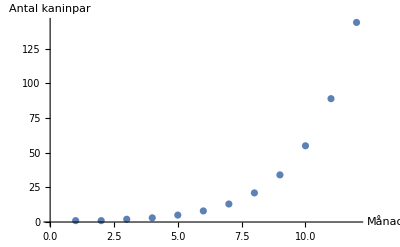

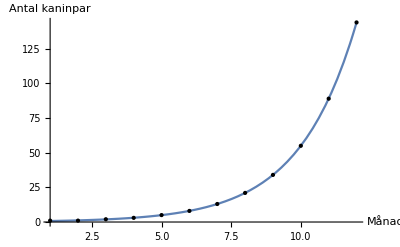
Vi anpassar sedan en exponentiell funktion f(n)=a e^(b n) efter värdena genom att använda funktionen FindFit, och skapar en ny graf:
-Graphics-

b. Vi ritar upp graf för funktionen för antalet kaninpar med en logaritmisk y-axel med hjälp av LogPlot:

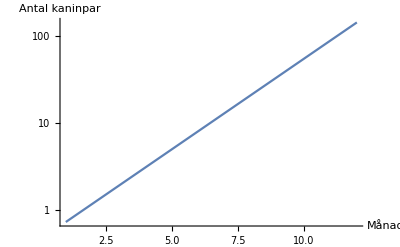

c. Mellan varje tidssteg n och n+1 ökar tillväxthastigheten och antalet kaninpar i enlighet med  p_(n+2)=p_(n+1)+p_n. Funktionen ökar exponentiellt eftersom första tidsderivatan (hastigheten) på funktionen är växande, samt att andraderivatan är positiv.

d. För uppgift d tog vi hjälp av kursens lärare Fadil Galjic. Vi ritar upp graferna för antalet kaninpar enligt Fibonacci-modellen samt en modell med en korrektionsfaktor k (“K-modellen”). K-modellen tas fram med hjälp av Mathematicas funktion DSolve, vilket ger resultatet:
K(n)=((x0*ⅇ^(r*t) k)/(-x0+x0*ⅇ^(r*t)+k))
Vi använder värdena för a och b som vi kom fram till i uppgift a, så att x0 = a och r=b. 
Sedan ritar vi upp en graf för K-modellen och Fibonaccis modell, där vi kan variera korrektionsfaktorn k. Med hjälp av denna graf kan vi sedan bestämma giltighetsområdet för Fibonaccis modell.  Grafen visar att Fibonaccis modell är giltig i ungefär 15 månader när k = 15 000.

Graf med Fibonaccis modell (blå), K-modellen (grön) och värdet på k (orange)

### Kod

```mathematica
FibonacciList=Table[Fibonacci[n],{n,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

```mathematica
antalManader = 12;
```

```mathematica
ListPlot[FibonacciList, AxesLabel->{"Månad","Antal kaninpar"}]
```

-Graphics-

```mathematica
transpose=Transpose[{Table[n,{n,1,antalManader}],FibonacciList}]
```

{{1,1},{2,1},{3,2},{4,3},{5,5},{6,8},{7,13},{8,21},{9,34},{10,55},{11,89},{12,144}}

```mathematica
graf=a*Exp[b*n]
```

a ⅇ^(b n)

```mathematica
graffit=FindFit[transpose,graf,{a,b},n]
```

{a→0.447396,b→0.481176}

```mathematica
a=0.4473959819804562;
```

```mathematica
b=0.48117600155393997;
```

```mathematica
antalKaniner=Function[{n},Evaluate[graf/.graffit]]
```

Function[{n},0.447396 ⅇ^(0.481176 n)]

```mathematica
Plot[antalKaniner[n],{n,1,antalManader},Epilog->Map[Point,transpose],AxesLabel->{"Månad","Antal kaninpar"}]
```

-Graphics-

```mathematica
LogPlot[antalKaniner[n],{n,1,antalManader},AxesLabel->{"Månad","Antal kaninpar"}]
```

-Graphics-

```mathematica
x0 = a;
r=b;
```

```mathematica
maxAntalManader = 20;
```

```mathematica
maxK = 15000;
minK = 100;
```

```mathematica
Manipulate[Plot[{antalKaniner[t],k,((x0*ⅇ^(r*t) k)/(-x0+x0*ⅇ^(r*t)+k))}, {t, 0, maxAntalManader} ],{k, minK, maxK}]
```

Graf med Fibonaccis modell (blå), K-modellen (grön) och värdet på k (orange)